```mathematica
Clear[measureDistance];

measureDistance[image_]:=Manipulate[DynamicModule[{pts={},x1=Null,x2=Null,ΔX,X1,X2,g,myRound},myRound[x_]:=Round[1000*x]/1000//N;
(*Begins the column with all the content of the manipulate*)Column[{(*Begin LocatorPane*)Dynamic@LocatorPane[Union[Dynamic[pts]],Dynamic@Show[{Image[image,ImageSize->size],Graphics[{color,AbsoluteThickness[lineThickness],Opacity[opacity],Line[Union[pts]]}]}],LocatorAutoCreate->True,(*Begin Locator appearance*)Appearance->If[whiteLocatorRing,Graphics[{{color,AbsoluteThickness[thickness],Circle[{0,0},radius+thickness/2]},{White,AbsoluteThickness[thickness],Circle[{0,0},radius]}},ImageSize->10],Graphics[{{color,AbsoluteThickness[thickness],Circle[{0,0},radius+thickness/2]}},ImageSize->10]](*End Locator appearance*)],(*End LocatorPane*)(*Begin of the block of InputFields*)Row[{Style["\!\(\*SubscriptBox[\(x\), \(1\)]\):"],InputField[Dynamic[x1],FieldHint->"Type  \!\(\*SubscriptBox[\(x\), \(1\)]\)",FieldSize->7,FieldHintStyle->{Red}],Spacer[20],Style["   \!\(\*SubscriptBox[\(x\), \(2\)]\):"],InputField[Dynamic[x2],FieldHint->"Type  \!\(\*SubscriptBox[\(x\), \(2\)]\)",FieldSize->7,FieldHintStyle->{Red}],(*Begin button "Memorize scale X"*)Spacer[30],Button["Memorize scale",X1=Min[Transpose[myRound/@Union[pts]][[1]]];
X2=Max[Transpose[myRound/@Union[pts]][[1]]];
ΔX=X2-X1;](*End of button "Memorize scale X"*)}],(*End of the block of InputFields and button*)Spacer[20],(*Begin button "Make the list of the curve's points"*)Button[Style["Pick up the locators coordinates and calculate the distance between them",Bold],g[{a_,b_}]:={(x1*X2-x2*X1)/ΔX+a/ΔX*Abs[x2-x1],(x1*X2-x2*X1)/ΔX+b/ΔX*Abs[x2-x1]};
Clear[poinTs,diStance];
poinTs=Map[myRound,Map[g,pts]];
diStance=poinTs//Differences//Norm],(*End of button "Make the list..."*)Row[{Style["Locators coordinates:      ",14,Blue,Bold],InputField[Dynamic[poinTs]]}],Spacer[10],Row[{Style["The inter-locator distance: ",14,Blue,Bold],InputField[Dynamic[diStance]]}]},Alignment->Center](*End of column with all the content of the manipulate*)],(*End of the DynamicModule*)(*The massive of sliders begins*)Column[{Row[{Control[{whiteLocatorRing,{True,False}}],Spacer[50]}],Row[{Spacer[32.35],Control[{{size,450},300,800}],Spacer[38.5],Control[{{opacity,0.5},0,1}]}],Row[{Spacer[10.],Control[{{thickness,1},0.5,5}],Spacer[13.65],Control[{{lineThickness,1},0,10}]}],Row[{Spacer[22.8],Control[{color,Red}],Spacer[59.3],Control[{{radius,0.5},0,3}]}]},Alignment->Center],(*The massive of sliders ends*)(*Definitions of sliders*)ControlType->{Checkbox,Slider,Slider,Slider,Slider,ColorSlider,Slider},ControlPlacement->Top,SaveDefinitions->True];

measureDistance[Image[-Graphics-,ImageSize->300]]
```

```mathematica
data1={{82,},{247,},{358,},{548,},{752,}};
```

Test code//

```mathematica
(*dataMg={{82,2.0979},{247,1.419089036},{358,1.40100573},{548,1.339559},{752,1.350095}};
nlm=NonlinearModelFit[dataMg,{a+b *x+c*x^2+d*x^3},{a,b,c,d},x];

nlm//Normal
(*{a->0.0740508,b->-0.00391526,c->1.0714}*)

Show[Plot[nlm[x],{x,10,800},PlotRange->All],ListPlot[dataMg,PlotStyle->Directive[Red,PointSize[0.02]]]]*)
```

Test code//

```mathematica
(*data={{82,2.0979},{247,1.419089036},{358,1.40100573},{548,1.339559},{752,1.350095}};
f=BSplineFunction[data];
Filling->{1->{2}};
f[.7];
Show[Graphics[{Red,Point[data],Green,Line[data]},Axes->True],
ParametricPlot[{f[t]},{t,0,1},PlotStyle->{{Thick,Blue}}],AspectRatio->1/GoldenRatio,Frame->True,Ticks->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]*)
```

Correct code::

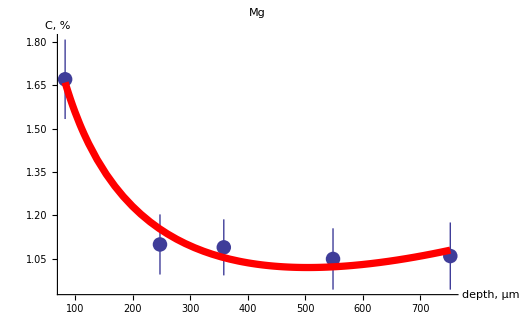

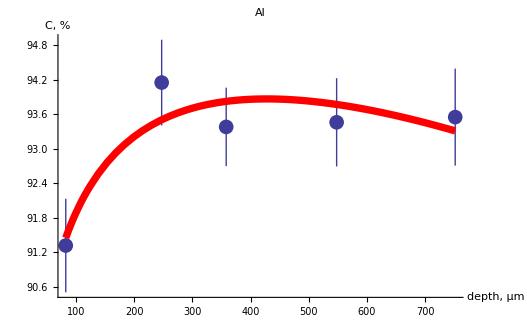

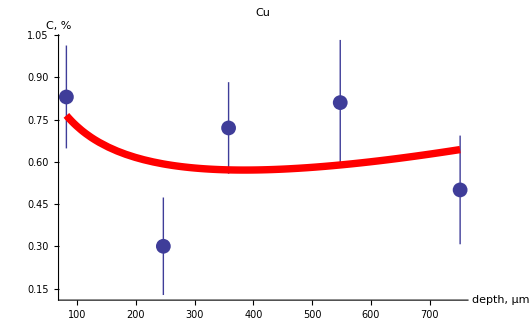

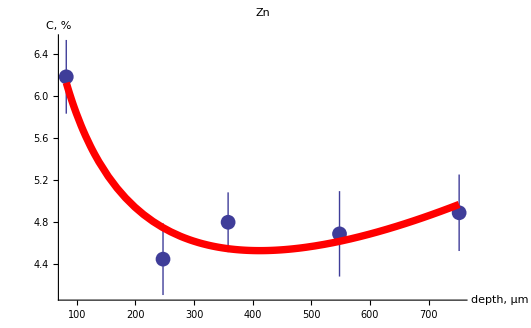

```mathematica
Needs["ErrorBarPlots`"]
dataMg={{82,1.67},{247,1.10},{358,1.09},{548,1.05},{752,1.06}};
ErdataMg={{{82,1.67},ErrorBar[1.67*8.21/100]},{{247,1.10},ErrorBar[1.10*9.43/100]},{{358,1.09},ErrorBar[1.09*8.87/100]},{{548,1.05},ErrorBar[1.05*10.07/100]},{{752,1.06},ErrorBar[1.06*10.93/100]}};
dataAl={{82,91.32},{247,94.15},{358,93.38},{548,93.46},{752,93.55}};
ErdataAl={{{82,91.32},ErrorBar[91.32*0.89/100]},{{247,94.15},ErrorBar[94.15*0.79/100]},{{358,93.38},ErrorBar[93.38*0.73/100]},{{548,93.46},ErrorBar[93.46*0.82/100]},{{752,93.55},ErrorBar[93.55*0.90/100]}};
dataCu={{82,0.83},{247,0.30},{358,0.72},{548,0.81},{752,0.50}};
ErdataCu={{{82,0.83},ErrorBar[0.83*22.00/100]},{{247,0.30},ErrorBar[0.30*57.69/100]},{{358,0.72},ErrorBar[0.72*22.57/100]},{{548,0.81},ErrorBar[0.81*27.46/100]},{{752,0.50},ErrorBar[0.50*38.58/100]}};
dataZn={{82,6.18},{247,4.45},{358,4.80},{548,4.69},{752,4.89}};
ErdataZn={{{82,6.18},ErrorBar[6.18*5.66/100]},{{247,4.45},ErrorBar[4.45*7.65/100]},{{358,4.80},ErrorBar[4.80*5.91/100]},{{548,4.69},ErrorBar[4.69*8.64/100]},{{752,4.89},ErrorBar[4.89*7.42/100]}};

pMg[x_]=Fit[dataMg,{1,x,Log[x]},x];
pMgIfStat[x_]:=If[x>82&&x<752,pMg[x]];
pAl[x_]=Fit[dataAl,{1,x,Log[x]},x];
pAlIfStat[x_]:=If[x>82&&x<752,pAl[x]];
pCu[x_]=Fit[dataCu,{1,x,Log[x]},x];
pCuIfStat[x_]:=If[x>82&&x<752,pCu[x]];
pZn[x_]=Fit[dataZn,{1,x,Log[x]},x];
pZnIfStat[x_]:=If[x>82&&x<752,pZn[x]];
gMgIfStat=Plot[pMgIfStat[x],{x,0,dataMg[[Length[dataMg],1]]},PlotRange->All,PlotStyle->{Red,Thickness[0.01]}];
gAlIfStat=Plot[pAlIfStat[x],{x,0,dataAl[[Length[dataAl],1]]},PlotRange->All,PlotStyle->{Red,Thickness[0.01]}];
gCuIfStat=Plot[pCuIfStat[x],{x,0,dataCu[[Length[dataCu],1]]},PlotRange->All,PlotStyle->{Red,Thickness[0.01]}];
gZnIfStat=Plot[pZnIfStat[x],{x,0,dataZn[[Length[dataZn],1]]},PlotRange->All,PlotStyle->{Red,Thickness[0.01]}];
(*dotsMg=ListPlot[dataMg,PlotStyle->{PointSize[0.02]},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Style["Mg",23],AxesLabel->{Style["depth, µm",18],Style["C, %",18]},AxesStyle->Directive[12,Arrowheads[{0,0.05}]]];
dotsAl=ListPlot[dataAl,PlotStyle->{PointSize[0.02]},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Style["Al",23],AxesLabel->{Style["depth, µm",18],Style["C, %",18]},AxesStyle->Directive[12,Arrowheads[{0,0.05}]]];
dotsCu=ListPlot[dataCu,PlotStyle->{PointSize[0.02]},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Style["Cu",23],AxesLabel->{Style["depth, µm",18],Style["C, %",18]},AxesStyle->Directive[12,Arrowheads[{0,0.05}]]];
dotsZn=ListPlot[dataZn,PlotStyle->{PointSize[0.02]},PlotRange->All,AxesOrigin->{25,0},PlotLabel->Style["Zn",23],Axes->True,AxesLabel->{Style["depth, µm",18],Style["C, %",18]},Frame->{True,True,False,False},FrameLabel->{Style["depth, µm",18],Style["C, %",18]},FrameStyle->Directive[12,Arrowheads[{0,0.05}]]];*)

ErdotsMg=ErrorListPlot[ErdataMg,PlotStyle->{PointSize[0.02]},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Style["Mg",23],AxesLabel->{Style["depth, µm",18],Style["C, %",18]},AxesStyle->Directive[12,Arrowheads[{0,0.05}]]];

ErdotsAl=ErrorListPlot[ErdataAl,PlotStyle->{PointSize[0.02]},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Style["Al",23],AxesLabel->{Style["depth, µm",18],Style["C, %",18]},AxesStyle->Directive[12,Arrowheads[{0,0.05}]]];
ErdotsCu=ErrorListPlot[ErdataCu,PlotStyle->{PointSize[0.02]},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Style["Cu",23],AxesLabel->{Style["depth, µm",18],Style["C, %",18]},AxesStyle->Directive[12,Arrowheads[{0,0.05}]]];
ErdotsZn=ErrorListPlot[ErdataZn,PlotStyle->{PointSize[0.02]},PlotRange->All,AxesOrigin->{0,0},PlotLabel->Style["Zn",23],AxesLabel->{Style["depth, µm",18],Style["C, %",18]},AxesStyle->Directive[12,Arrowheads[{0,0.05}]]];

(*Show[dotsMg,gMgIfStat]*)
Show[ErdotsMg,gMgIfStat]

(*Show[dotsAl,gAlIfStat]*)
Show[ErdotsAl,gAlIfStat]

(*Show[dotsCu,gCuIfStat]*)
Show[ErdotsCu,gCuIfStat]

(*Show[dotsZn,gZnIfStat]*)
Show[ErdotsZn,gZnIfStat]
```

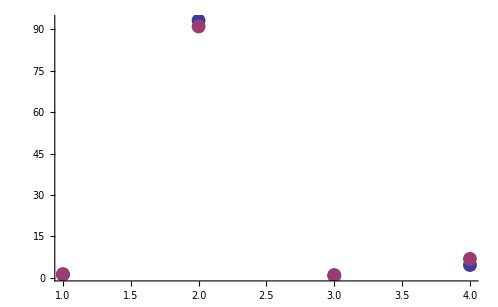

```mathematica
dataNO={{1,1.16},{2,93.25},{3,0.97},{4,4.63}};
dataNO2={{1,1.34},{2,91.07},{3,0.72},{4,6.87}};
(*ErdataNO2={{{"",},ErrorBar[/100]},{{1,},ErrorBar[/100]},{{1,},ErrorBar[/100]},{{1,},ErrorBar[/100]}};*)
ListPlot[{dataNO,dataNO2},PlotStyle->{PointSize[0.02]},PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
-Graphics-//ColorNegate
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»